#### One Chain

```mathematica
FoldList[BitXor,Range[100]]
```

{1,3,0,4,1,7,0,8,1,11,0,12,1,15,0,16,1,19,0,20,1,23,0,24,1,27,0,28,1,31,0,32,1,35,0,36,1,39,0,40,1,43,0,44,1,47,0,48,1,51,0,52,1,55,0,56,1,59,0,60,1,63,0,64,1,67,0,68,1,71,0,72,1,75,0,76,1,79,0,80,1,83,0,84,1,87,0,88,1,91,0,92,1,95,0,96,1,99,0,100}

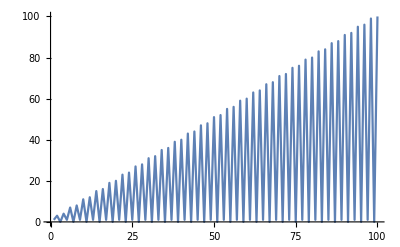

```mathematica
ListLinePlot[%]
```

```mathematica
FoldList[BitXor,Table[11,40]]
```

{11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0,11,0}

```mathematica
FoldList[BitXor,Range[100]]
```

{1,3,0,4,1,7,0,8,1,11,0,12,1,15,0,16,1,19,0,20,1,23,0,24,1,27,0,28,1,31,0,32,1,35,0,36,1,39,0,40,1,43,0,44,1,47,0,48,1,51,0,52,1,55,0,56,1,59,0,60,1,63,0,64,1,67,0,68,1,71,0,72,1,75,0,76,1,79,0,80,1,83,0,84,1,87,0,88,1,91,0,92,1,95,0,96,1,99,0,100}

Decoding:

```mathematica
BitXor@@@Partition[%,2,1]
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

#### Two Chains

```mathematica
{Range[50],Reverse[Range[50]]}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50},{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}}

```mathematica
ArrayPlot[CellularAutomaton[60,RandomInteger[1,300],200]]
```

-Graphics-

#### Overall

```mathematica
(* Fold[Fold[BitXor, #] &, datavec] *)
```

```mathematica
FoldList
```

```mathematica
enc[datavec]->
```

```mathematica
RandomInteger[1,{10,5}]//Column
```

{0,0,0,1,0}
{0,0,1,1,0}
{0,1,1,0,1}
{1,0,1,0,1}
{1,1,0,0,0}
{1,1,0,0,1}
{0,1,1,0,0}
{1,0,0,0,0}
{1,1,1,1,1}
{0,1,1,0,1}

```mathematica
idata=RandomInteger[1,{10,5}]
```

{{1,0,0,1,0},{1,1,1,0,0},{0,0,1,1,1},{0,0,1,1,1},{0,1,1,1,1},{0,0,1,1,1},{1,0,1,1,0},{1,1,1,0,0},{1,0,1,1,0},{0,1,1,1,1}}

```mathematica
FoldList[BitXor,idata]
```

{{1,0,0,1,0},{0,1,1,1,0},{0,1,0,0,1},{0,1,1,1,0},{0,0,0,0,1},{0,0,1,1,0},{1,0,0,0,0},{0,1,1,0,0},{1,1,0,1,0},{1,0,1,0,1}}

```mathematica
FoldList[BitXor,#]&/@%
```

{{1,1,1,0,0},{0,1,0,1,1},{0,1,1,1,0},{0,1,0,1,1},{0,0,0,0,1},{0,0,1,0,0},{1,1,1,1,1},{0,1,0,0,0},{1,0,0,1,1},{1,1,0,0,1}}

```mathematica
Table[Take[Range[40],n;;-1;;4],{n,4}]//Column
```

{1,5,9,13,17,21,25,29,33,37}
{2,6,10,14,18,22,26,30,34,38}
{3,7,11,15,19,23,27,31,35,39}
{4,8,12,16,20,24,28,32,36,40}

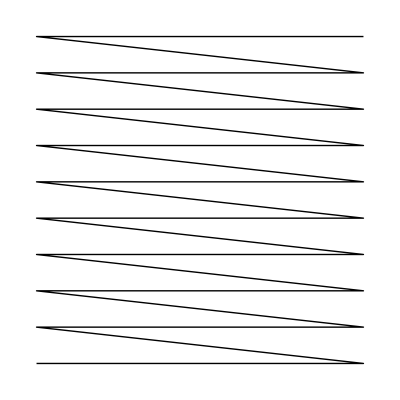

```mathematica
Graphics[Line[Table[FirstPosition[Table[Take[Range[100],n;;-1;;10],{n,10}],i],{i,100}]]]
```

```mathematica
Grid[Table[Take[Range[15^2],n;;-1;;15],{n,15}]]
```

1 | 16 | 31 | 46 | 61 | 76 | 91 | 106 | 121 | 136 | 151 | 166 | 181 | 196 | 211
2 | 17 | 32 | 47 | 62 | 77 | 92 | 107 | 122 | 137 | 152 | 167 | 182 | 197 | 212
3 | 18 | 33 | 48 | 63 | 78 | 93 | 108 | 123 | 138 | 153 | 168 | 183 | 198 | 213
4 | 19 | 34 | 49 | 64 | 79 | 94 | 109 | 124 | 139 | 154 | 169 | 184 | 199 | 214
5 | 20 | 35 | 50 | 65 | 80 | 95 | 110 | 125 | 140 | 155 | 170 | 185 | 200 | 215
6 | 21 | 36 | 51 | 66 | 81 | 96 | 111 | 126 | 141 | 156 | 171 | 186 | 201 | 216
7 | 22 | 37 | 52 | 67 | 82 | 97 | 112 | 127 | 142 | 157 | 172 | 187 | 202 | 217
8 | 23 | 38 | 53 | 68 | 83 | 98 | 113 | 128 | 143 | 158 | 173 | 188 | 203 | 218
9 | 24 | 39 | 54 | 69 | 84 | 99 | 114 | 129 | 144 | 159 | 174 | 189 | 204 | 219
10 | 25 | 40 | 55 | 70 | 85 | 100 | 115 | 130 | 145 | 160 | 175 | 190 | 205 | 220
11 | 26 | 41 | 56 | 71 | 86 | 101 | 116 | 131 | 146 | 161 | 176 | 191 | 206 | 221
12 | 27 | 42 | 57 | 72 | 87 | 102 | 117 | 132 | 147 | 162 | 177 | 192 | 207 | 222
13 | 28 | 43 | 58 | 73 | 88 | 103 | 118 | 133 | 148 | 163 | 178 | 193 | 208 | 223
14 | 29 | 44 | 59 | 74 | 89 | 104 | 119 | 134 | 149 | 164 | 179 | 194 | 209 | 224
15 | 30 | 45 | 60 | 75 | 90 | 105 | 120 | 135 | 150 | 165 | 180 | 195 | 210 | 225

```mathematica
array=Table[Take[Range[15^2],n;;-1;;15],{n,15}];
```

## 2D CA?

```mathematica
Sort@{1123956776897,270361043509,3097483878567,1123289366095,277206003607,3681848058291}
```

{270361043509,277206003607,1123289366095,1123956776897,3097483878567,3681848058291}

```mathematica
ArrayPlot[CellularAutomaton[{1123289366095,3,1},RandomInteger[2,300],100]]
```

-Graphics-

```mathematica
Tuples[Range[0,2],4]
```

{{0,0,0,0},{0,0,0,1},{0,0,0,2},{0,0,1,0},{0,0,1,1},{0,0,1,2},{0,0,2,0},{0,0,2,1},{0,0,2,2},{0,1,0,0},{0,1,0,1},{0,1,0,2},{0,1,1,0},{0,1,1,1},{0,1,1,2},{0,1,2,0},{0,1,2,1},{0,1,2,2},{0,2,0,0},{0,2,0,1},{0,2,0,2},{0,2,1,0},{0,2,1,1},{0,2,1,2},{0,2,2,0},{0,2,2,1},{0,2,2,2},{1,0,0,0},{1,0,0,1},{1,0,0,2},{1,0,1,0},{1,0,1,1},{1,0,1,2},{1,0,2,0},{1,0,2,1},{1,0,2,2},{1,1,0,0},{1,1,0,1},{1,1,0,2},{1,1,1,0},{1,1,1,1},{1,1,1,2},{1,1,2,0},{1,1,2,1},{1,1,2,2},{1,2,0,0},{1,2,0,1},{1,2,0,2},{1,2,1,0},{1,2,1,1},{1,2,1,2},{1,2,2,0},{1,2,2,1},{1,2,2,2},{2,0,0,0},{2,0,0,1},{2,0,0,2},{2,0,1,0},{2,0,1,1},{2,0,1,2},{2,0,2,0},{2,0,2,1},{2,0,2,2},{2,1,0,0},{2,1,0,1},{2,1,0,2},{2,1,1,0},{2,1,1,1},{2,1,1,2},{2,1,2,0},{2,1,2,1},{2,1,2,2},{2,2,0,0},{2,2,0,1},{2,2,0,2},{2,2,1,0},{2,2,1,1},{2,2,1,2},{2,2,2,0},{2,2,2,1},{2,2,2,2}}

```mathematica
Graph[#->CellularAutomaton[{1123289366095,3,1}][#]&/@Tuples[Range[0,2],4]]
```

-Graphics-

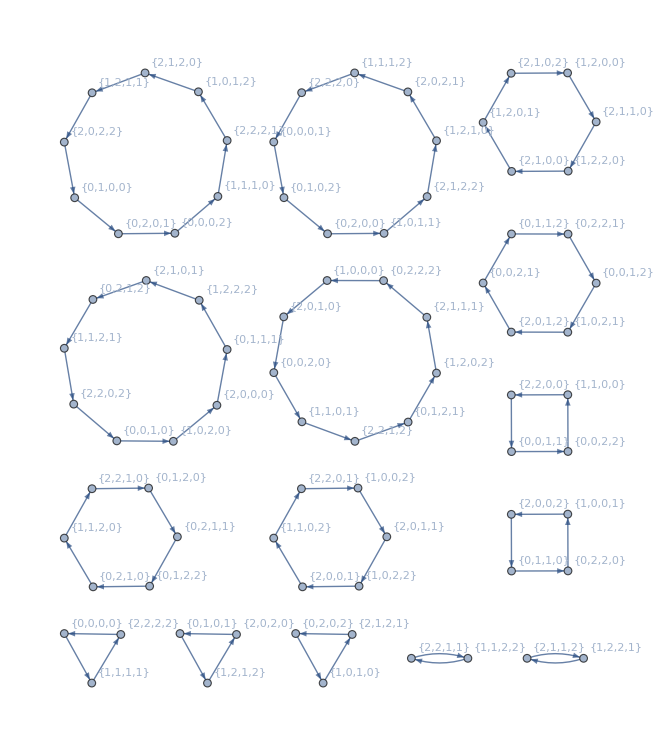

```mathematica
Graph[#->CellularAutomaton[{1123289366095,3,1}][#]&/@Tuples[Range[0,2],4],VertexLabels->Automatic]
```

Not a reversible rule:

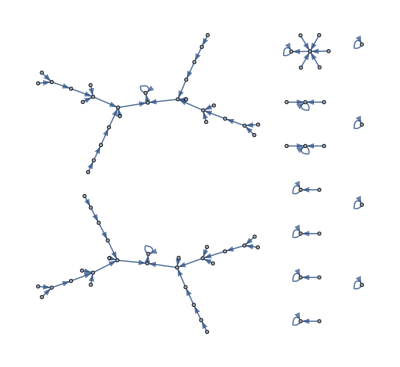

```mathematica
Graph[#->CellularAutomaton[{11232893095,3,1}][#]&/@Tuples[Range[0,2],4]]
```

```mathematica
ArrayPlot[CellularAutomaton[{1123289366095,3,1},{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{1123289366095,3,1},{{1,2,1},0},100]]
```

-Graphics-

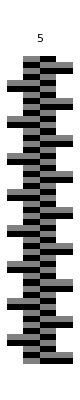
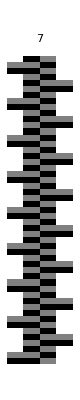
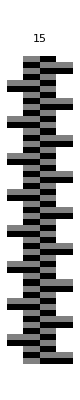
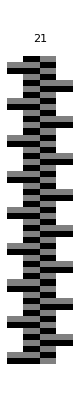
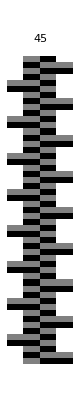
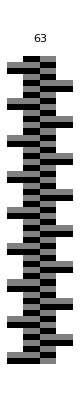
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ArrayPlot[CellularAutomaton[{1123289366095,3,1},{IntegerDigits[n,3],0},50],PlotLabel->n,ImageSize->Tiny],{n,100}]
```

## FoldList[BitXor]

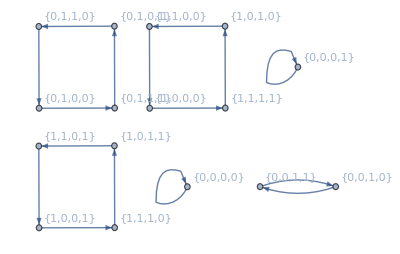

```mathematica
Graph[#->FoldList[BitXor,#]&/@Tuples[Range[0,1],4],VertexLabels->Automatic]
```

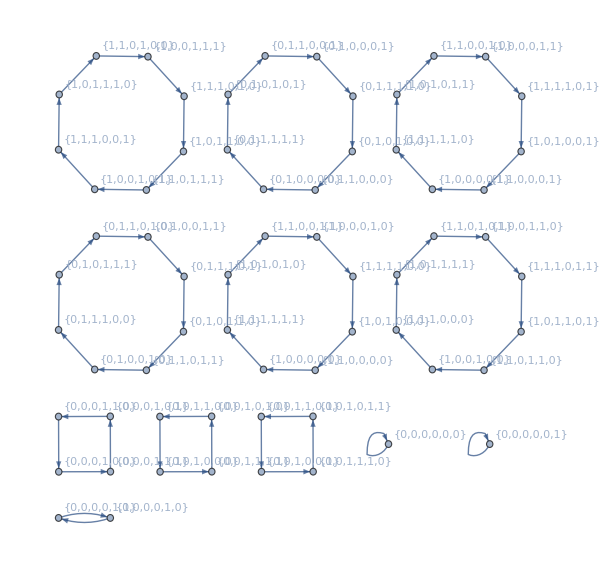

```mathematica
Graph[#->FoldList[BitXor,#]&/@Tuples[Range[0,1],6],VertexLabels->Automatic]
```

## Rough Encoding/Decoding

```mathematica
ArrayPlot[CellularAutomaton[150,{RandomInteger[1,30],0},200]]
```

-Graphics-